```mathematica
DynamicModule[{g}, Dynamic[g], Initialization:>(g = RandomGraph[{10,10}, VertexLabels->"Name", VertexShapeFunction->(EventHandler[Disk[#1, .02],"MouseClicked":>(g=VertexDelete[g,#2])]&)];)]
```

```mathematica
DynamicModule[{g}, Dynamic[g], Initialization:>(g = RandomGraph[{20,20}, VertexLabels->"Name", VertexShapeFunction->(EventHandler[Disk[#1, .09],"MouseClicked":>(g=HighlightGraph[g, NeighborhoodGraph[g,v,2]] )]&)];)]
```

```mathematica
g3 = RandomGraph[{15,15}, VertexLabels->"Name"]
HighlightGraph[g3,Pick[EdgeList[g3],DegreeCentrality[g3],2]]
```

```mathematica
F1[x_,y_]:=Sin[x] Cos[y];
g5[t_]:=t;
g6[t_]:=Cos[t];
```

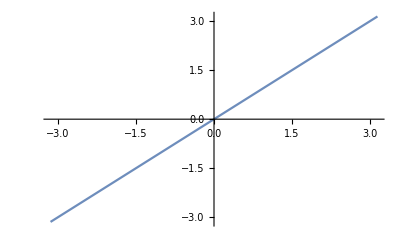

```mathematica
sur=Plot[{x},{x,-Pi,Pi},Mesh->None,PlotStyle->Opacity[0.9]]
```

```mathematica
Animate[Show[sur,Plot[{g5[u],g6[u],F1[g5[u]]},{u,-Pi,endu},PlotStyle->Thick]],{endu,-Pi,Pi}]
```